# Test NNTracePlot

These tests require the standard test file resources folder to be downloaded from Git and available at Tests/_resources.

Updated 20160608

## Initialization

```mathematica
<<NounouW`
```

HokahokaW`
Thu 9 Jun 2016 10:43:35     [Mathematica: 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)]
     Current local repository path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [126533ea69146d2bf85bdf97b6ec768a9cbcc322]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

NounouW`
Thu 9 Jun 2016 10:43:35     [Mathematica: 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)]
     Current local repository path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  master [e13f72bf504f0a08f8a6fef57c6efb1b301dec98]
     Remote:  origin (https://github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

Welcome to nounou, a Scala/Java adapter for neurophysiological data.\nLast GIT info from file resource: NNGit.gson.txt\n  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e\n  + current branch is: master\n  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git\n

```mathematica
resourceDataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]], "_resources","nounou","Neuralynx"}]
```

C:\prog\_w\NounouW\NounouW\Tests\_resources\nounou\Neuralynx

```mathematica
FileExistsQ[resourceDataDirectory]
```

True

```mathematica
(*ShowJavaConsole[]*)
```

## BG001 (short snippet)

```mathematica
tempDataFiles=FileNames["*.ncs",FileNameJoin[{resourceDataDirectory,"BG001","2016-05-11_16-34-20", "split","t0508_001", "segment 1","1-1"}]];
```

```mathematica
testBG001 = NNLoad[tempDataFiles]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
NNPrintInfo[ testBG001, "Timing" ]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	      2560 (  0:00.08) (     0.1)	  3401478496 ( 0:00.00)

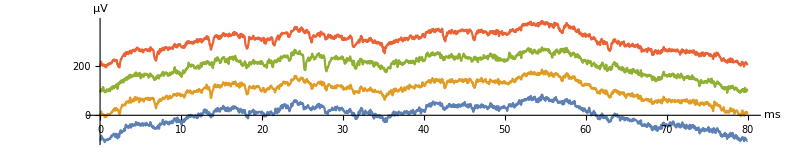

```mathematica
NNTracePlot[ testBG001, All, All, NNOptStack-> 100, AspectRatio-> 1/5, ImageSize-> 72*11]
```

## NCS1 (SPP010: single channel, many segments)

```mathematica
testNCS1 = NNLoad[ FileNameJoin[{resourceDataDirectory,"SPP010","2013-12-02_17-07-31",#}]& /@{"Tet4a.ncs","Tet4b.ncs","Tet4c.ncs","Tet4d.ncs"} ]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
NNPrintInfo[ testNCS1, "Timing" ]
```

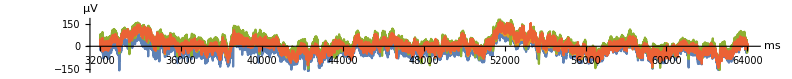

```mathematica
NNTracePlot[testNCS1, All, { 32001;;64000,0}, AspectRatio-> 1/10, ImageSize->11*72, NNOptStack-> None]
```

### Timing information

```mathematica
testNCS1@getTiming[]@toString[]
```

NNTiming(fs=32000.0, segmentCount=1)

```mathematica
NNPrintInfo[testNCS1]
```

nounou.elements.data.NNDataChannelArray(1 segments, fs=32000.0,  , 1a58c41332)
NNTiming(fs=32000.0, segmentCount=1)

NNDataChannelArray(1 segments, fs=32000.0,

```mathematica
NNPrintInfo[testNCS1, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
================================================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	 151597056 ( 78:57.41) (  4737.4)	 19228868023 ( 0:00.00)

### Specifying time ranges

```mathematica
testRange@segment[]
```

0

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ {10 ;; 20, 0}];
{testRange, NNReadTimepoints[testNCS1,testRange ]}
```

{«JavaObject[nounou.ranges.NNRange]»,{19228868336,19228868367,19228868398,19228868429,19228868461,19228868492,19228868523,19228868554,19228868586,19228868617,19228868648}}

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ {10 ;; 20 ;;5, 0}];
{testRange, NNReadTimepoints[ testNCS1 ,testRange]}
```

{«JavaObject[nounou.ranges.NNRange]»,{19228868336,19228868492,19228868648}}

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ 19228868492 -> 0;; 10];
{testRange, NNReadTimepoints[ testNCS1 ,testRange]}
```

{«JavaObject[nounou.ranges.NNRangeTsEvent]»,{19228868492,19228868523,19228868554,19228868586,19228868617,19228868648,19228868679,19228868711,19228868742,19228868773,19228868804}}

```mathematica
testRange=$NNSpanToNNRangeSpecifier[ {19228868492, 19228868648} -> 0;; 10];
{testRange, NNReadTimepoints[  testNCS1, # ]& /@ testRange}
```

{{«JavaObject[nounou.ranges.NNRangeTsEvent]»,«JavaObject[nounou.ranges.NNRangeTsEvent]»},{{19228868492,19228868523,19228868554,19228868586,19228868617,19228868648,19228868679,19228868711,19228868742,19228868773,19228868804},{19228868648,19228868679,19228868711,19228868742,19228868773,19228868804,19228868836,19228868867,19228868898,19228868929,19228868961}}}

### NNReadTrace

```mathematica
testData=NNReadTrace[testNCS1,0,{ 32001;;64000,0} ];
```

```mathematica
ListLinePlot[testData, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### NNDataDownsample

```mathematica
testNCS1Downsample = NNDataDownsample[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Downsample ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Downsample,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### NNDataDecimate

```mathematica
testNCS1Decimate = NNDataDecimate[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Decimate ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Decimate,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### Whole Range Plot